```mathematica
(* These are the eigenfunctions for the harmonic oscillator *)
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
(* This is the two-body ground state for two fermions in a harmonic trap *)
Subscript[ψ, F][x_,y_] = 1/Sqrt[2] * (Subscript[ϕ, 0][x]Subscript[ϕ, 1][y] - Subscript[ϕ, 0][y]Subscript[ϕ, 1][x] );
(* One-body density matrix for fermionic two-body ground state *)
Subscript[ρ, F][x_,y_] = Integrate[Subscript[ψ, F][x,Subscript[x, 2]]*Subscript[ψ, F][y,Subscript[x, 2]], {Subscript[x, 2],-∞, ∞}]
(* OBDM for hard-core anyons in two-body g.s. See LaTex note for derivation explaining why this expression is the OBDM for hard-core anyons *)
Subscript[ρ, A][x_,y_,κ_]=Subscript[ρ, F][x,y]-Sign[y-x]*(E^(-Sign[y-x]*I*π*κ)+1)*Integrate[Subscript[ψ, F][x,Subscript[x, 2]]*Subscript[ψ, F][y,Subscript[x, 2]], {Subscript[x, 2],x, y}]
```

(ⅇ^(-x^2/2-y^2/2) (1+2 x y))/(2 √π)

(ⅇ^(-x^2/2-y^2/2) (1+2 x y))/(2 √π)-(ⅇ^(-3/2 (x^2+y^2)) (1+ⅇ^(-ⅈ π κ Sign[-x+y])) (2 ⅇ^(x^2) x+ⅇ^(y^2) (-2 y+ⅇ^(x^2) √π (1+2 x y) (-Erf[x]+Erf[y]))) Sign[-x+y])/(4 π)

```mathematica
(* 
Ξ is function that projects the OBDM onto the harmonic oscillator eigenbasis by creating matrix of size (n+1)x(n+1)
		
n -- integer designating desired size of the matrix (e.g., n=5 will output a  6 x 6 matrix, corresponding to projections onto the first 6 harmonic oscillator
κ -- anyonic parameter;
 *)
Subscript[Ξ, n_,κ_]:=Round[Table[NIntegrate[Subscript[ϕ, l][x] * Subscript[ϕ, m][y]*Subscript[ρ, A][x,y,κ],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->10,PrecisionGoal->10],{l, 0,n},{m,0,n}],10^(-10)];
(* S uses Ξ matrix to calculate von Neumann Entropy 

This function is not very readable because it has a lot of nested functions, but this is what it does

1. Finds eigenvalues of matrix Subscript[Ξ, n,κ]
2. Rounds the eigenvalues so that any eigenvalues that are very close to 0 but not 0 will be set to 0
3. Removes any eigenvalues that are equal to 0 (otherwise we could not take the logarithm of each eigenvalue)
4. Finds the sum Subscript[Σ^∞, i] Subscript[λ, i]* Log[Subscript[λ, i]]
*)
Subscript[S, n_,κ_]:=(-DeleteCases[Round[  Eigenvalues[Subscript[Ξ, n,κ]], 10^(-15)]   , 0 ].Transpose[{Log[DeleteCases[Round[  Eigenvalues[Subscript[Ξ, n,κ]], 10^(-15)] , 0 ]]}] )[[1]]//N;
```

```mathematica
Do[Subscript[Ξ, 5,n/10]=Subscript[Ξ, 5,n/10],{n,0,20}]
```

```mathematica
(* After each matrix has been found and saved, use those results to find the entropy for each κ, creating an array of values of S *)
SP=Array[Subscript[S, 5,#/10]&,21,0]
```

{0.653596,0.654832,0.658395,0.663864,0.670581,0.677713,0.684345,0.6896,0.692797,0.6937,0.693147,0.6937,0.692797,0.6896,0.684345,0.677713,0.670581,0.663864,0.658395,0.654832,0.653596}

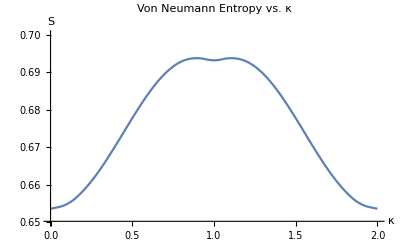

```mathematica
(* Viewing the list of S values above, there is indeed a dip at κ = 1 when S goes from 0.6937 to 0.693147 back to 06937 *)
(* This higher value S = 0.6937 occurs for κ = 9/10 *)
ListLinePlot[Thread[{Range[0,2,1/10], SP}],InterpolationOrder->2,PlotRange->{.65,.7},PlotLabel->"Von Neumann Entropy vs. κ",AxesLabel->{"κ","S"}]
```

```mathematica
(*  To determine whether this dip is a numerical error, I have increased the matrix cutoff size for κ = 9/10 to see if that solves the issue *)
(* Increasing the matrix cutoff size changes S in the fourth decimal place, but in fact increases the entropy S  *)
Subscript[Ξ, 6,9/10]=Subscript[Ξ, 6,9/10];
Subscript[Ξ, 6,9/10]//N//MatrixForm
Eigenvalues[Subscript[Ξ, 6,9/10]]//N
Subscript[S, 6,9/10]
```

(0.505335 | 0.-0.043586 ⅈ | 0.00477013 | 0.-0.00889696 ⅈ | -0.000459006 | 0.+0.00298413 ⅈ | 0.0000558685
0.+0.043586 ⅈ | 0.491843 | 0.+0.03082 ⅈ | -0.000918013 | 0.-0.00444848 ⅈ | 0.000342123 | 0.+0.00121827 ⅈ
0.00477013 | 0.-0.03082 ⅈ | 0.00224866 | 0. | -0.000432755 | 0. | 0.00015802
0.+0.00889696 ⅈ | -0.000918013 | 0. | 0.000249852 | 0. | -0.000111737 | 0.
-0.000459006 | 0.+0.00444848 ⅈ | -0.000432755 | 0. | 0.000124926 | 0. | -0.0000608219
0.-0.00298413 ⅈ | 0.000342123 | 0. | -0.000111737 | 0. | 0.0000582987 | 0.
0.0000558685 | 0.-0.00121827 ⅈ | 0.00015802 | 0. | -0.0000608219 | 0. | 0.0000351643)

{0.543835,0.455507,0.000411929,0.000123728,0.0000142649,1.74538×10^-6,1.66972×10^-7}

0.693949

```mathematica
(* One possibility is that I have not set the accuracy/precision goal high enough, so in the next cell I have redone the calculation with a higher accuracy/precision goal to make sure the numerical result is stable *)
Subscript[Ξ, n_,κ_]:=Round[Table[NIntegrate[Subscript[ϕ, l][x] * Subscript[ϕ, m][y]*Subscript[ρ, A][x,y,κ],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->12,PrecisionGoal->12],{l, 0,n},{m,0,n}],10^(-13)];
Subscript[Ξ, 6,9/10]=.
```

```mathematica
(* Subscript[Ξ, 6,9/10] has been cleared in the previous cell and the function reset to higher accuracy/precision *)
Subscript[Ξ, 6,9/10]=Subscript[Ξ, 6,9/10];
Subscript[Ξ, 6,9/10]//N//MatrixForm
Eigenvalues[Subscript[Ξ, 6,9/10]]//N
Subscript[S, 6,9/10]
```

(0.505335 | 0.-0.043586 ⅈ | 0.00477013 | 0.-0.00889696 ⅈ | -0.000459006 | 0.+0.00298413 ⅈ | 0.0000558685
0.+0.043586 ⅈ | 0.491843 | 0.+0.03082 ⅈ | -0.000918013 | 0.-0.00444848 ⅈ | 0.000342123 | 0.+0.00121827 ⅈ
0.00477013 | 0.-0.03082 ⅈ | 0.00224866 | 0. | -0.000432755 | 0. | 0.00015802
0.+0.00889696 ⅈ | -0.000918013 | 0. | 0.000249851 | 0. | -0.000111737 | 0.
-0.000459006 | 0.+0.00444848 ⅈ | -0.000432755 | 0. | 0.000124926 | 0. | -0.0000608219
0.-0.00298413 ⅈ | 0.000342123 | 0. | -0.000111737 | 0. | 0.0000582987 | 0.
0.0000558685 | 0.-0.00121827 ⅈ | 0.00015802 | 0. | -0.0000608219 | 0. | 0.0000351643)

{0.543835,0.455507,0.000411929,0.000123728,0.0000142649,1.74538×10^-6,1.66982×10^-7}

0.693949

```mathematica
(* Even after increasing the accuracy/precision goals, the value for S does not change in the first 6 decimal places, so the dip does not seem to be a result of insufficiently accurate numerics *)
```